```mathematica
f[x_]:=(4275)*((Sin[Pi*0.1*Sin[(x-4)/500]/(0.000546)]*(0.000546/(Pi*0.1*Sin[(x-4)/500])))^2)*(Cos[Pi*0.406*Sin[(x-4)/500]/0.000546]^2);
Table[f[x],{x,0,8,0.05}]
```

Data file Importing:

```mathematica
AppendTo[$Path,"Desktop/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"Users/emulder/GitHub/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"Users/ilipart/GitHub/PhotonInterferenceLab/Analysis"];
data2Slit = Import["4.45mmAll.csv"];
dataFarSlit = Import["4mmAll.csv"];
dataNearSlit = Import["5.9mmAll.csv"];
data2SlitAvg = Import["4.45mmAvg.csv"];
dataFarSlitAvg = Import["4mmAvg.csv"];
dataNearSlitAvg = Import["5.9mmAvg.csv"];
data2SlitError = Import["4.45mmError.csv"];
dataFarSlitError = Import["4mmError.csv"];
dataNearSlitError = Import["5.9mmError.csv"];
```

Fraunhofer Model for double slit and single slit: fit comparison with data and parameter optimization

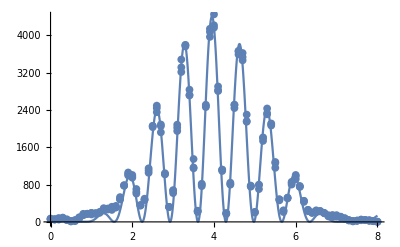

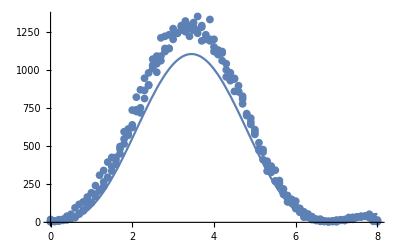

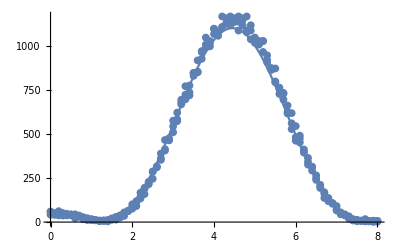

```mathematica
g[x_]:= I0*((Sin[Pi*a*Sin[(x-x0)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x0)/D2])))^2)*(Cos[Pi*d*Sin[(x-x0)/D2]/lambda]^2)+c;
I0 = 4400;
a = 0.085;
d = 0.406;
lambda = 0.000555;
x0 = 3.95;
c = 3.6;
D1=500;
D2=500;
fit = Plot[g[x],{x,0,8}];
dataPlot2Slit = ListPlot[data2Slit,PlotMarkers->{Automatic,8}];
Show[fit,dataPlot2Slit]

h[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x1)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x1)/D2])))^2)+c;
x1 = 3.45;
fit2 = Plot[h[x],{x,0,8},PlotRange->All];
dataPlotFarSlit = ListPlot[dataFarSlit,PlotMarkers->{Automatic,8}];
Show[fit2,dataPlotFarSlit]

k[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x2)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x2)/D2])))^2)+c;
x2 = 4.45;
fit3 = Plot[k[x],{x,0,8},PlotRange->All];
dataPlotNearSlit = ListPlot[dataNearSlit,PlotMarkers->{Automatic,8}];
Show[fit3,dataPlotNearSlit]
```

Fresnel Model for double slit and single slit: fit comparison with data and parameter optimization

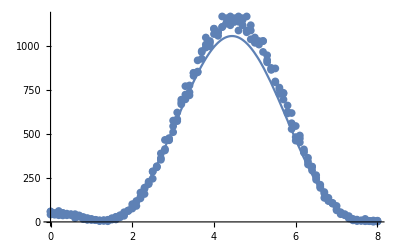

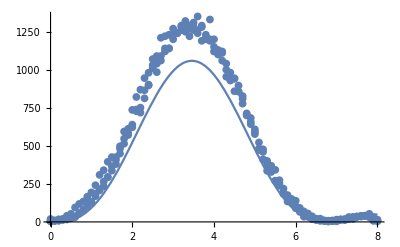

```mathematica
slit1[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0+(d/2),x0+(d/2)+a}]
s1[z_]:=33.3*I0*Re[slit1[z]*Conjugate[slit1[z]]]
slit2[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0-(d/2)-a,x0-(d/2)}]
s2[z_]:=33.3*I0*Re[slit2[z]*Conjugate[slit2[z]]]
fitb=Plot[s1[z],{z,0,8},PlotRange->All];
fitc=Plot[s2[z],{z,0,8},PlotRange->All];
Show[fitb,dataPlotNearSlit]
Show[fitc,dataPlotFarSlit]
```

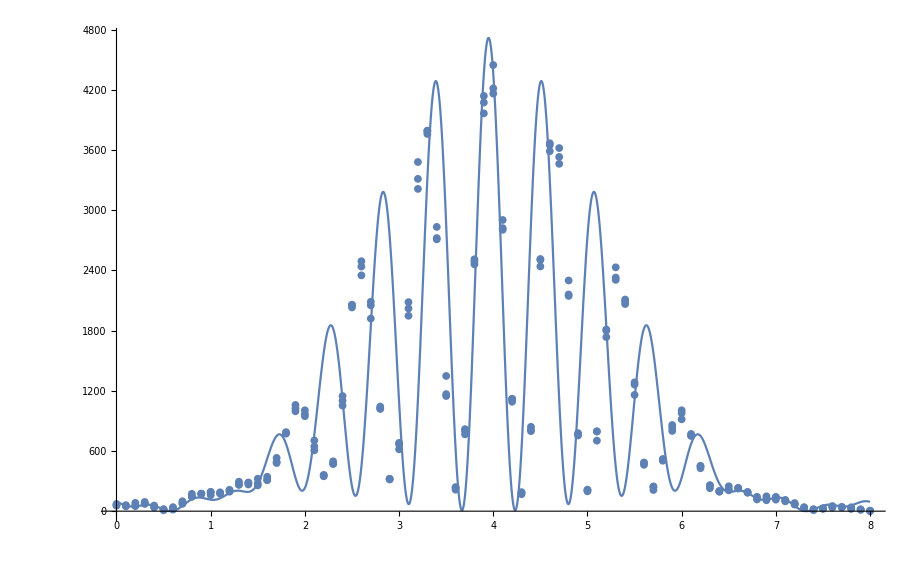

```mathematica
slitdouble[z_]:=slit1[z]+slit2[z]
slit[z_]:=40*I0*Re[slitdouble[z]*Conjugate[slitdouble[z]]]
fita=Plot[slit[z],{z,0,8}];
Show[fita,dataPlot2Slit]
```